```mathematica
a=1
ra=1
R10=(2*a^{-3/2}*Exp[-x/a])
Plot[R10,{x, 0, 10}]
```

```mathematica
R20=((1/Sqrt[2])*a^{-3/2}*(1-(x/(2*a)))*Exp[-x/(2*a)])
R21=((1/Sqrt[24])*a^{-3/2}*(x/a)*Exp[-x/(2*a)])
R30=((2/Sqrt[27])*a^{-3/2}*(1-((2*x)/(3*a))+(2/27)*(x/a)^{2})*Exp[-x/(3*a)])
R31=((8/(27*Sqrt[6]))*a^{-3/2}*(1- (x/(6*a)))*(x/a)*Exp[-x/(3*a)])
```

{(ⅇ^(-x/2) (1-x/2))/(√2)}

{(ⅇ^(-x/2) x)/(2 √6)}

{(2 ⅇ^(-x/3) (1-(2 x)/3+(2 x^2)/27))/(3 √3)}

{4/27 √(2/3) ⅇ^(-x/3) (1-x/6) x}

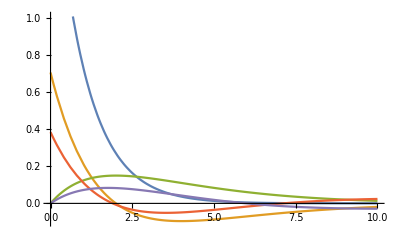

```mathematica
Plot[{R10, R20, R21, R30,R31}, {x,0,10}, PlotRange->{-0.1,1.01}]
```

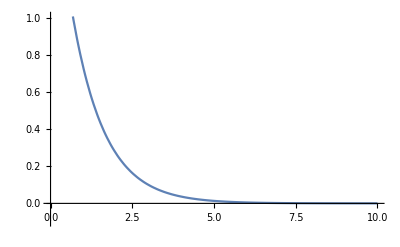

```mathematica
Plot[R10, {x,0,10}, PlotRange->{-0.1,1.01}]
```

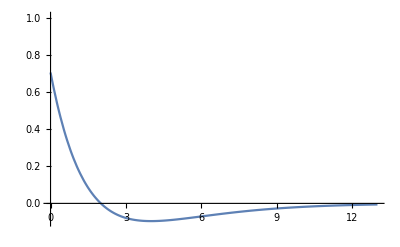

```mathematica
Plot[R20, {x,0,13}, PlotRange->{-0.1,1.01}]
```

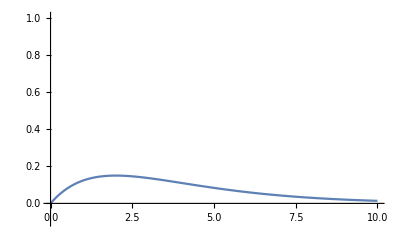

```mathematica
Plot[R21, {x,0,10}, PlotRange->{-0.1,1.01}]
```

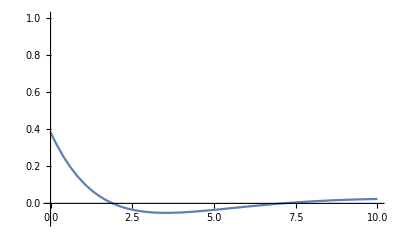

```mathematica
Plot[R30, {x,0,10}, PlotRange->{-0.1,1.01}]
```

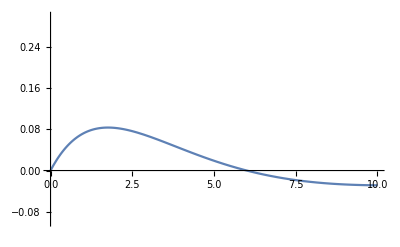

```mathematica
Plot[R31, {x,0,10}, PlotRange->{-0.1,0.3}]
```

1

3

0

(ⅇ^(-x/3) (6-6 x+x^2))/(54 √3)

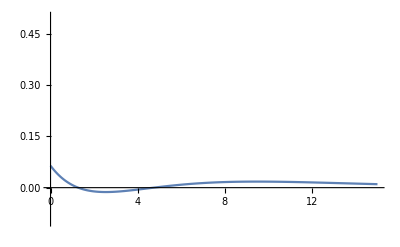

```mathematica
(*Desarrollo completo de la función de onda *)
a0 = 1  (*Radio de Bohr*)
n= 3
l =0
Raiz[n_, l_]:= Sqrt[(2/(n a0))^3  (Factorial[n-l-1]/(2 n (Factorial[n+l])^3)) ]
F[n_,l_,x_]:= Exp[-x/(n a0)] ((2 x)/(n a0))^l LaguerreL[n-l-1,2 l+1,x]
G=Raiz[n,l]*F[n,l,x]
Plot[G,{x,0,15},PlotRange->{-0.1,0.5}]
```